## Reproducing the purification sequence with gates derived from the hamiltonian

This notebook explores the purification sequence by simulating the hamiltonian (in secular approximation).
We aim to synthesize the following gate sequence. With the assumption that we generate a perfect state on the electron spins (i.e. V=1)
-Graphics-

```mathematica
Quiet[Needs["QDENSITY`Qdensity`"]];
Quiet[Needs["QDENSITY`QCWave`"]];
?QDENSITY`Qdensity`*
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

General useful definitions such as gates etc.

```mathematica
KP[r__]:=KroneckerProduct[r]
StyleNumber[number_] :=Style[number,Bold,Darker[Green]]
Stokesfromρ[ρ_]:=(t =Table[Re[Tr[Subscript[σ, i].ρ]],{i,1,3}]//N; t)
StokesfromρStyled[ρ_]:=(t =Table[If[Abs[Re[Tr[Subscript[σ, i].ρ]]]>0.4,StyleNumber[Re[Tr[Subscript[σ, i].ρ]]],Re[Tr[Subscript[σ, i].ρ]]],{i,1,3}]//N; t)
ρfromψ[ψ_] :=ψ.ψ†;
Stokesfromψ[ψ_]:=Stokesfromρ[ρfromψ[ψ]];
Fidfromρ[ρ_,σ_]:=Re[Tr[MatrixPower[MatrixPower[ρ,0.5].σ.MatrixPower[ρ,0.5],0.5]]^2];
MixedState=𝕀/2;(*Mixed state*)
transformAndNorm[state_,U_]:=(out=U.state.U†;out=out/Tr[out]);
measureOut[state_]:=KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†+KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†;
```

```mathematica
(*Single qubit gates*)
{rxp,rXp,ryp,rYp,rzp,rZp}=Table[AF[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[AF[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
rThetaX[θ_]=MatrixExp[-ⅈ*Subscript[σ, 1]*θ/2];
rThetaY[θ_]=MatrixExp[-ⅈ*Subscript[σ, 2]*θ/2];
rThetaZ[θ_]=MatrixExp[-ⅈ*Subscript[σ, 3]*θ/2];
rThetaϕ[θ_,ϕ_]=MatrixExp[-ⅈ*(Cos[ϕ] Subscript[σ, 1]*θ+Sin[ϕ] Subscript[σ, 2]*θ)/2];
```

Our nuclear spin parameters for both setups:

```mathematica
(ωL4-54)/(2π)
```

(-54+ωL4)/(2 π)

```mathematica
(*LT3*)
ωL3 = 2*π*447841.28;
Aperp3 =2*π*(87.5)*10^3;
Apar3 = -2*π*(30.0)*10^3 ;
par3 = ωL3+Apar3;

N3 = 12; (*original gate parameters*)
(*N3 = N3-2;(*adjusted for simulation in accuracies*)*)
τ3 = 10.886*10^-6; (*original gate parameters*)
(*τ3 = τ3 -29.1*10^-9;*)

(*LT4*)
ωL4 = 2*π*443172.12;
Aperp4 =2*π*(35.0)*10^3;
Apar4 =-2*π*(33.0)*10^3 ; (*because we use the -1 transition here*)
par4=Apar4+ωL4;
N4 = 34; (*original gate parameters*)
(*N4 = N4-2; (*adjust fdor simulation*)*)
τ4 = 6.406*10^-6(*original gate parameters*); 
(*τ4 =τ4+14*10^-9(*adjust for simulation*);*)


(*carbon parameters as a list*)
LT3Cinit = {ωL3,par3,Aperp3};
LT3Gate = {τ3,N3}; (*Gate parameters have to be slightly adjusted*)
LT4Cinit={ωL4,par4+7500,1};
LT4C=LT4Cinit;
LT4C[[3]]=Sqrt[(2π 416572.34)^2-LT4C[[2]]^2];
LT4Gate = {τ4,N4};(*Gate parameters have to be slightly adjusted*)

(*LT4C={ωL4,par4+12000,1};
LT4C[[3]]=Sqrt[(2π 416572.34)^2-LT4C[[2]]^2];
*)
LT4C={ωL4,par4+35000,1};
LT4C[[3]]=Sqrt[(2π 416572.34)^2-LT4C[[2]]^2];

LT4C={ωL4,par4+36500,1};
LT4C[[3]]=Sqrt[(2π 416572.34)^2-LT4C[[2]]^2];
```

The system Hamiltonian with NV and Carbon reads

```mathematica
Usys[t_,{ω_,par_,Aperp_}] := MatrixExp[-ⅈ t/2(ω KP[Subscript[𝒫, 0],Subscript[σ, 3]]+KP[Subscript[𝒫, 1],((par)Subscript[σ, 3]+Aperp*Subscript[σ, 1])])];
```

Import the pulse sequences

```mathematica
getPulses[basedir_,measname_]:=Module[{i,importSeq,numGroups,headings,seqOverview,PulseSeqs},
importSeq=Import[basedir<>measname<>"/"<>"sequence_overview.csv"];
seqOverview=importSeq[[2;;]];
numGroups=Dimensions[seqOverview][[1]];
PulseSeqs={};
For[i=1,i<=numGroups,i++,PulseSeqs=Append[PulseSeqs,Import[basedir<>measname<>"/"<>seqOverview[[i,1]]<>".csv"][[2;;]]]];
Transpose[{seqOverview,PulseSeqs}]]
```

```mathematica
basedir = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/";
```

In the compiled sequences, 0 encodes Y gate, π/2 encodes X gate, 3 π/2 encodes - X gate, π encodes - Y gate

```mathematica
compiledPulse[{ω_,Apar_,Aperp_},pulseData_,scaleFact_:1,ignoreFinal_:False]:=Module[{i,numPulses,evMat,pulseMat,pulseDelay,compiledPulse},
numPulses=Dimensions[pulseData[[2]]][[1]];
compiledPulse=IdentityMatrix[4];
For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1,scaleFact pulseData[[2,i,1]],scaleFact(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];
evMat=Usys[pulseDelay,{ω,Apar,Aperp}];
pulseMat=If[pulseData[[2,i,5]]==0,KP[rThetaϕ[pulseData[[2,i,4]],(π/2-pulseData[[2,i,3]])],Subscript[σ, 0]],KP[Subscript[𝒫, 0],Subscript[σ, 0]]];
compiledPulse=pulseMat.evMat.compiledPulse;
];
pulseDelay=If[Not[ignoreFinal],scaleFact(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];
compiledPulse=Usys[pulseDelay,{ω,Apar,Aperp}].compiledPulse;
Return[compiledPulse]
]
```

## Carbon calib

```mathematica
(*(*numPoints =Dimensions[LT4phase][[1]]/3;
phase=-60+Range[0,numPoints-1]*(460./(numPoints-1));
MeasVals={};
For[i=1,i≤numPoints,i++,
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4phase[[3(i-1)+2]],scaleFactLT4];
MeasLT4=compiledPulse[LT4C,LT4phase[[3(i-1)+3]],scaleFactLT4];
pulse=MeasLT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];]
Clear[x];
nlmLT4=NonlinearModelFit[Transpose[{phase,MeasVals}],Amp*Cos[2π f x-a]+off,{{f,1/360},{a,2π},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[{Transpose[{phase,MeasVals}]},Joined->{False}],Plot[Normal[nlmLT4],{x,phase[[1]],phase[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]];
aout=180/π If[Amp>0,Mod[a,2π],Mod[a+π,2π]]/.nlmLT4["BestFitParameters"]
aout-180*)


(*InitLT4Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[2]]];
InitEAndSwapLT4SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[3]]];
InitEAndSwapLT4SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapY[[3]]];
InitEAndSwapLT4SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapZ[[3]]];
InitSwap={InitEAndSwapLT4SwapX,InitEAndSwapLT4SwapY,InitEAndSwapLT4SwapZ};
TomoLT4XSwapX=compiledPulse[LT4C,LT4SwapX[[4]]];
TomoLT4XSwapY=compiledPulse[LT4C,LT4SwapX[[8]]];
TomoLT4XSwapZ=compiledPulse[LT4C,LT4SwapX[[12]]];
TomoSwap={TomoLT4XSwapZ,TomoLT4XSwapY,TomoLT4XSwapX};
For[i=1,i≤3,i++,Print["Input: "<>Basis[[i]]];
pulseLT3=TomoSwap[[i]].InitSwap[[i]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT3]];
Print[Re[Tr[Subscript[σ, 3].outState]]]]*)*)
```

```mathematica
(*LT4msm0C=getPulses[basedir, "AWG_seqs_msm0_freq_C4_Pulses"];*)
```

```mathematica
(*LT4msm1C=getPulses[basedir, "AWG_seqs_msm1_freq_C4_Pulses"];*)
```

```mathematica
(*LT4phase=getPulses[basedir,"AWG_seqs_phase_C4_Pulses"];*)
```

```mathematica
(*LT4msm0C[[1;;10,1]]*)
```

```mathematica
(*numPoints =Dimensions[LT4msm0C][[1]]/3;
freeEvTime=400*^-6+Range[0,numPoints-1]*(1./16*^3);
MeasVals={};
For[i=1,i≤numPoints,i++,
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4msm0C[[3(i-1)+2]]];
MeasLT4=compiledPulse[LT4C,LT4msm0C[[3(i-1)+3]]];
pulse=MeasLT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];]

Clear[x];
nlmLT4=NonlinearModelFit[Transpose[{freeEvTime,MeasVals}],Amp*Cos[2π f x-a]+off,{{f,2*^3},{a,2π},{Amp,1},{off,0.5}},x];
Show[ListPlot[{Transpose[{freeEvTime,MeasVals}]},Joined->{False}],Plot[Normal[nlmLT4],{x,0,freeEvTime[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
f/.nlmLT4["BestFitParameters"]*)
```

```mathematica
(*LT4SwapX=getPulses[basedir,"AWG_seqs_elc_carb_swap_X_Pulses"];*)
```

```mathematica
(*LT4SwapY=getPulses[basedir,"AWG_seqs_elc_carb_swap_Y_Pulses"];*)
```

```mathematica
(*LT4SwapZ=getPulses[basedir,"AWG_seqs_elc_carb_swap_Z_Pulses"];*)
```

```mathematica
(*(*LT4C={ωL4-5.61*^3,par4+29120,Aperp4-45500};*)
LT4C={ωL4-54,par4+32520,Aperp4-20000};

numPoints =Dimensions[LT4msm1C][[1]]/3;
freeEvTime=400*^-6+Range[0,numPoints-1]*(1./16*^3);
MeasVals={};
For[i=1,i≤numPoints,i++,
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4msm1C[[3(i-1)+2]]];
MeasLT4=compiledPulse[LT4C,LT4msm1C[[3(i-1)+3]]];
pulse=MeasLT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];]
Clear[x];
nlmLT4=NonlinearModelFit[Transpose[{freeEvTime,MeasVals}],Amp*Cos[2π f x-a]+off,{{f,2*^3},{a,2π},{Amp,1},{off,0.5}},x];
plot1 =Show[ListPlot[{Transpose[{freeEvTime,MeasVals}]},Joined->{False}],Plot[Normal[nlmLT4],{x,0,freeEvTime[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}],ImageSize->Medium]
f/.nlmLT4["BestFitParameters"]

Basis={"X","Y","Z"};
InitLT4Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[2]]];
InitEAndSwapLT4SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[3]]];
InitEAndSwapLT4SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapY[[3]]];
InitEAndSwapLT4SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapZ[[3]]];
InitSwap={InitEAndSwapLT4SwapX,InitEAndSwapLT4SwapY,InitEAndSwapLT4SwapZ};
TomoLT4XSwapX=compiledPulse[LT4C,LT4SwapX[[4]]];
TomoLT4XSwapY=compiledPulse[LT4C,LT4SwapX[[8]]];
TomoLT4XSwapZ=compiledPulse[LT4C,LT4SwapX[[12]]];
TomoSwap={TomoLT4XSwapZ,TomoLT4XSwapY,TomoLT4XSwapX};
For[i=1,i≤3,i++,Print["Input: "<>Basis[[i]]];
pulseLT3=TomoSwap[[i]].InitSwap[[i]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT3]];
Print[Re[Tr[Subscript[σ, 3].outState]]]]*)
```

```mathematica
LT4phase=getPulses[basedir,"AWG_seqs_phase_C4_Pulses"];
```

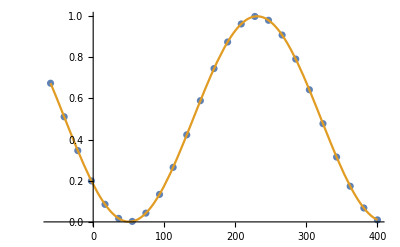

129.55

```mathematica
LT4C={ωL4,par4+34349.1,1};
LT4C[[3]]=Sqrt[(2π 416572.34)^2-LT4C[[2]]^2];

numPoints =Dimensions[LT4phase][[1]]/3;
phase=-60+Range[0,numPoints-1]*(460./(numPoints-1));
MeasVals={};
For[i=1,i≤numPoints,i++,
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4phase[[3(i-1)+2]],1];
MeasLT4=compiledPulse[LT4C,LT4phase[[3(i-1)+3]],1];
pulse=MeasLT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];]
Clear[x];
nlmLT4=NonlinearModelFit[Transpose[{phase,MeasVals}],Amp*Cos[2π (f x+a/360)]+off,{{f,1/360},{a,0},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[{Transpose[{phase,MeasVals}]},Joined->{False}],Plot[Normal[nlmLT4],{x,phase[[1]],phase[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
aout=If[Amp>0,Mod[a,360],Mod[a+180,360]]/.nlmLT4["BestFitParameters"]
```

## Simulate swap gate

```mathematica
LT4SwapX=getPulses[basedir,"AWG_seqs_elc_carb_swap_X_Pulses"];
```

```mathematica
LT4SwapY=getPulses[basedir,"AWG_seqs_elc_carb_swap_Y_Pulses"];
```

```mathematica
LT4SwapZ=getPulses[basedir,"AWG_seqs_elc_carb_swap_Z_Pulses"];
```

```mathematica
LT4SwapX[[;;,1]]
```

(MBI_0 | True | MBI_0 | init_C4_y_pt0_tau_0_N_0 | 0.000029756
init_C4_y_pt0_tau_0_N_0 | False | MBI_0 | init_E_y_pt0_tau_0_N_0 | 0.000967248
init_E_y_pt0_tau_0_N_0 | False | MBI_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.0009708
Tomo_y_pi2_init0_tau_0_N_0 | True | MBI_1 | init_C4_y_pt1_tau_0_N_0 | 0.000478044
MBI_1 | True | MBI_1 | init_C4_y_pt1_tau_0_N_0 | 0.000478044
init_C4_y_pt1_tau_0_N_0 | False | MBI_1 | init_E_y_pt1_tau_0_N_0 | 0.000967248
init_E_y_pt1_tau_0_N_0 | False | MBI_1 | Tomo_y_pi2_init1_tau_0_N_0 | 0.0009708
Tomo_y_pi2_init1_tau_0_N_0 | True | MBI_2 | init_C4_y_pt2_tau_0_N_0 | 0.00047748
MBI_2 | True | MBI_2 | init_C4_y_pt2_tau_0_N_0 | 0.00047748
init_C4_y_pt2_tau_0_N_0 | False | MBI_2 | init_E_y_pt2_tau_0_N_0 | 0.000967248
init_E_y_pt2_tau_0_N_0 | False | MBI_2 | phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0.0009708
phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | False | None | None | 0.000885228)

```mathematica
InitLT4Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[2]]];

InitEAndSwapLT4SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[3]]];
InitEAndSwapLT4SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapY[[3]]];
InitEAndSwapLT4SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapZ[[3]]];

InitSwap={InitEAndSwapLT4SwapX,InitEAndSwapLT4SwapY,InitEAndSwapLT4SwapZ};

TomoLT4XSwapX=compiledPulse[LT4C,LT4SwapX[[4]]];
TomoLT4XSwapY=compiledPulse[LT4C,LT4SwapX[[8]]];
TomoLT4XSwapZ=compiledPulse[LT4C,LT4SwapX[[12]]];

TomoSwap={TomoLT4XSwapX,TomoLT4XSwapY,TomoLT4XSwapZ};
```

```mathematica
pulseLT3=InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT3]]
```

(0.998532+0. ⅈ | 0.0351821+0.00585294 ⅈ
0.0351821-0.00585294 ⅈ | 0.00146845+0. ⅈ)

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];For[i=1,i≤3,i++,
pulseLT3=TomoSwap[[i]].InitSwap[[j]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT3]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]]
```

Input: X

X 0.000918591

Y -0.0710881

Z 0.991544

Input: Y

X -0.00724499

Y -0.997057

Z -0.0366998

Input: Z

X 0.999613

Y 0.00229112

Z -0.11937

Carrying on with rest of sequence

## Check classical correlations

### LT4

```mathematica
ClassCorLT4X=getPulses[basedir,"AWG_seqs_classical_correlations_onC13_X_Pulses"];
```

```mathematica
ClassCorLT4X[[1;;6,1]]
ClassCorLT4X[[83;;89,1]]
```

(C_Init4_y_pt0_tau_0_N_0 | False | C_Init4_y_pt0_tau_0_N_0 | LDE10 | 0.000977248
LDE10 | False | C_Init4_y_pt0_tau_0_N_0 | LDE20 | 0.000985448
LDE20 | False | None | LDE_rephasing_2_0 | 7.×10^-6
LDE_rephasing_2_0 | False | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.392×10^-6
Single_C13_Phase_correct0_0_DD_elt_tau_2298_N_2 | False | None | Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | 9.192×10^-6
Single_C13_Phase_correct0_1_DD_elt_tau_2298_N_2 | False | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.192×10^-6)

(Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | False | Purify_y_pi2_init0_tau_0_N_0 | None | 8.192×10^-6
Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | False | None | None | 0.000010192
Purify_y_pi2_init0_tau_0_N_0 | False | Tomo1_y_pi2_init0_tau_0_N_0 | Tomo0_y_pi2_init0_tau_0_N_0 | 0.0005358
Tomo0_y_pi2_init0_tau_0_N_0 | False | Rome_0 | None | 0.000454568
Tomo1_y_pi2_init0_tau_0_N_0 | False | None | None | 0.000454368
C_Init4_y_pt1_tau_0_N_0 | False | C_Init4_y_pt1_tau_0_N_0 | LDE11 | 0.00143162
LDE11 | False | C_Init4_y_pt1_tau_0_N_0 | LDE21 | 0.000985448)

```mathematica
ClassCorLT4Y=getPulses[basedir,"AWG_seqs_classical_correlations_onC13_Y_Pulses"];
ClassCorLT4Z=getPulses[basedir,"AWG_seqs_classical_correlations_onC13_Z_Pulses"];
```

Check that the pulses match:

```mathematica
For[z=1,z<=Dimensions[ClassCorLT4X][[1]],z++,If[ClassCorLT4X[[z,2]]!=ClassCorLT4Y[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[ClassCorLT4X][[1]],z++,If[ClassCorLT4X[[z,2]]!=ClassCorLT4Z[[z,2]],Print[z]]]
```

2

89

176

2

89

176

```mathematica
ClassCorLT4X[[2,2]]==ClassCorLT4X[[89,2]]
ClassCorLT4X[[2,2]]==ClassCorLT4X[[176,2]]
```

True

True

```mathematica
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4Z[[1]]];
LDESwapLT4X=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4X[[2]]];
LDESwapLT4Y=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4Y[[2]]];
LDESwapLT4Z=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4Z[[2]]];
LDE2LT4=compiledPulse[LT4C,ClassCorLT4Z[[3]]];
rephasingLT4=compiledPulse[LT4C,ClassCorLT4Z[[4]]];
c13PhaseCorEvenLT4=compiledPulse[LT4C,ClassCorLT4Z[[5]]];
c13PhaseCorOddLT4=compiledPulse[LT4C,ClassCorLT4Z[[6]]];
c13FinalCorEvenLT4=compiledPulse[LT4C,ClassCorLT4Z[[83]]];
c13FinalCorOddLT4=compiledPulse[LT4C,ClassCorLT4Z[[84]]];
PurLT4=compiledPulse[LT4C,ClassCorLT4Z[[85]]];
TomoLT4X=compiledPulse[LT4C,ClassCorLT4Y[[86]]];
TomoLT4Y=compiledPulse[LT4C,ClassCorLT4Y[[173]]];
TomoLT4Z=compiledPulse[LT4C,ClassCorLT4Y[[260]]];
TomoLT4Xmin=compiledPulse[LT4C,ClassCorLT4Z[[87]]];
TomoLT4Ymin=compiledPulse[LT4C,ClassCorLT4Z[[174]]];
TomoLT4Zmin=compiledPulse[LT4C,ClassCorLT4Z[[261]]];

TotalPhaseCompGateLT4[n_]:=If[Mod[n,2]==0,c13FinalCorOddLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,n/2],
c13FinalCorEvenLT4.c13PhaseCorEvenLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,(n-1)/2]]
inits={LDESwapLT4X,LDESwapLT4Y,LDESwapLT4Z};
tomos={TomoLT4X,TomoLT4Y,TomoLT4Z};
tomosMin={TomoLT4Xmin,TomoLT4Ymin,TomoLT4Zmin};
bases={"X","Y","Z"};
```

```mathematica
pulseLT4=InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.998532+0. ⅈ | -0.0295592-0.0199572 ⅈ
-0.0295592+0.0199572 ⅈ | 0.00146845+0. ⅈ)

```mathematica
pulseLT4=LDESwapLT4Z.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.489555+0. ⅈ | -0.499441+0.0212106 ⅈ
-0.499441-0.0212106 ⅈ | 0.510445+0. ⅈ)

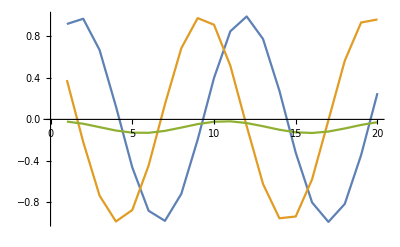

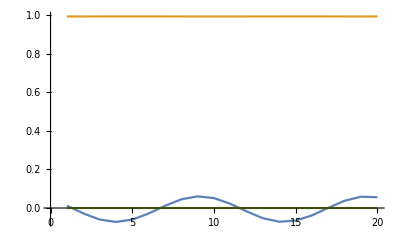

```mathematica
PhaseComp[n_]:=Module[{},pulseLT4=TotalPhaseCompGateLT4[n].rephasingLT4.LDE2LT4.LDESwapLT4Z.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
{Tr[Subscript[σ, 1].PTr[{1},outState]],Tr[Subscript[σ, 2].PTr[{1},outState]],Tr[Subscript[σ, 3].PTr[{1},outState]],Tr[Subscript[σ, 1].PTr[{2},outState]],Tr[Subscript[σ, 2].PTr[{2},outState]],Tr[Subscript[σ, 3].PTr[{2},outState]]}]
phaseCompSweep=Table[PhaseComp[n],{n,1,40,2}];
ListPlot[Transpose[phaseCompSweep][[1;;3]],Joined->True]
ListPlot[Transpose[phaseCompSweep][[4;;6]],Joined->True]
```

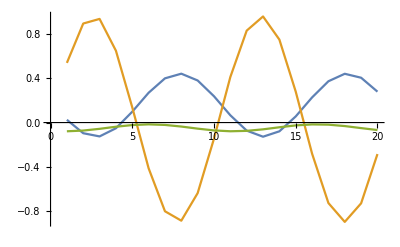

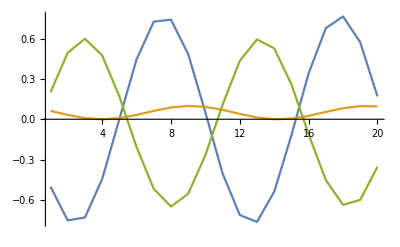

```mathematica
PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.LDE2LT4.SwapLT4.LDELT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
{Tr[Subscript[σ, 1].PTr[{1},outState]],Tr[Subscript[σ, 2].PTr[{1},outState]],Tr[Subscript[σ, 3].PTr[{1},outState]],Tr[Subscript[σ, 1].PTr[{2},outState]],Tr[Subscript[σ, 2].PTr[{2},outState]],Tr[Subscript[σ, 3].PTr[{2},outState]]}]
phaseCompSweep=Table[PhaseComp[n],{n,1,40,2}];
ListPlot[Transpose[phaseCompSweep][[1;;3]],Joined->True]
ListPlot[Transpose[phaseCompSweep][[4;;6]],Joined->True,PlotRange->All]
```

#### Calibrate phase offset

15

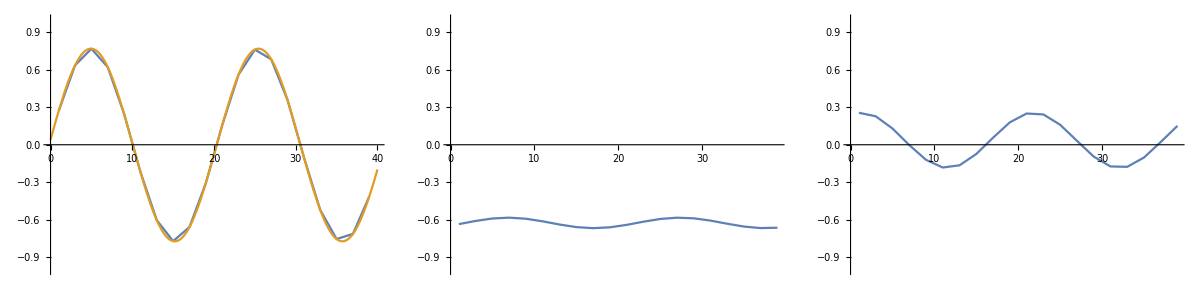

```mathematica
PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.LDE2LT4.LDESwapLT4Z.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
outState=measureOut[outState];
outState=transformAndNorm[outState,TomoLT4X];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
Clear[x,a];
nlmLT4=NonlinearModelFit[phaseCompSweep,Amp*Cos[2π f x-a]+off,{{f,1/20},{a,2π},{Amp,1},{off,0.5}},x];
xx=Show[ListPlot[phaseCompSweep,Joined->{True}],Plot[Normal[nlmLT4],{x,0,40},PlotStyle->{ColorData[97,"ColorList"][[2]]}],PlotRange->{Automatic,{-1,1}}];
offsetLT4=Round[If[Amp>0,Mod[a+π,2π],Mod[a,2π]]/(2π f)/.nlmLT4["BestFitParameters"]]

PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.LDE2LT4.LDESwapLT4Z.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
outState=measureOut[outState];
outState=transformAndNorm[outState,TomoLT4Y];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
yy=ListPlot[phaseCompSweep,Joined->{True},PlotRange->{Automatic,{-1,1}}];

PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.LDE2LT4.LDESwapLT4Z.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
outState=measureOut[outState];
outState=transformAndNorm[outState,TomoLT4Z];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
zz=ListPlot[phaseCompSweep,Joined->{True},PlotRange->{Automatic,{-1,1}}];

Grid[{{xx,yy,zz}}]
```

```mathematica
For[j=1,j≤3,j++,Print["Input " <>bases[[j]]];For[i=1,i≤3,i++,pulseLT4=tomos[[i]].KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4.LDE2LT4.inits[[j]].InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]]]]

Print["Min"]
For[j=1,j≤3,j++,Print["Input " <>bases[[j]]];For[i=1,i≤3,i++,pulseLT4=tomosMin[[i]].KP[Subscript[𝒫, 1],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4.LDE2LT4.inits[[j]].InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]]]]
```

Input X

X -0.0766088

Y -0.673023

Z 0.708448

Input Y

X 0.0187205

Y -0.99721

Z -0.09477

Input Z

X -0.733671

Y -0.664868

Z -0.206433

Min

Input X

X -0.068896

Y -0.657122

Z -0.770842

Input Y

X 0.106428

Y 0.975688

Z -0.155271

Input Z

X -0.811416

Y -0.581454

Z -0.0152647

## Purification

### LT4

```mathematica
PureLT4X=getPulses[basedir,"AWG_seqs_Purify_XX_Pulses"];
PureLT4Y=getPulses[basedir,"AWG_seqs_Purify_YY_Pulses"];
PureLT4Z=getPulses[basedir,"AWG_seqs_Purify_ZZ_Pulses"];
```

```mathematica
PureLT4X[[1;;9,1]]
PureLT4X[[86;;,1]]
```

(C_Init4_y_pt0_tau_0_N_0 | False | C_Init4_y_pt0_tau_0_N_0 | LDE10 | 0.000977248
LDE10 | False | None | LDE_rephasing_10 | 7.×10^-6
LDE1_final_0 | False | C_Init4_y_pt0_tau_0_N_0 | LDE_rephasing_10 | 7.×10^-6
LDE_rephasing_10 | False | C_Init4_y_pt0_tau_0_N_0 | LDE20 | 0.000978448
LDE20 | False | None | LDE_rephasing_2_0 | 7.×10^-6
LDE2_final_0 | False | C_Init4_y_pt0_tau_0_N_0 | LDE_rephasing_2_0 | 7.×10^-6
LDE_rephasing_2_0 | False | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.392×10^-6
Single_C13_Phase_correct0_0_DD_elt_tau_2298_N_2 | False | None | Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | 9.192×10^-6
Single_C13_Phase_correct0_1_DD_elt_tau_2298_N_2 | False | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.192×10^-6)

(Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | False | Purify_y_pi2_init0_tau_0_N_0 | None | 8.192×10^-6
Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | False | None | None | 0.000010192
Purify_y_pi2_init0_tau_0_N_0 | False | Tomo1_y_pi2_init0_tau_0_N_0 | Tomo0_y_pi2_init0_tau_0_N_0 | 0.0005358
Tomo0_y_pi2_init0_tau_0_N_0 | False | Rome_0 | None | 0.000454568
Tomo1_y_pi2_init0_tau_0_N_0 | False | None | None | 0.000454368)

```mathematica
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,PureLT4X[[1]]];
LDELT4=compiledPulse[LT4C,PureLT4X[[2]]];
SwapLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,PureLT4X[[4]]];
LDE2LT4=compiledPulse[LT4C,PureLT4X[[5]]];
rephasingLT4=compiledPulse[LT4C,PureLT4X[[7]]];
c13PhaseCorEvenLT4=compiledPulse[LT4C,PureLT4X[[8]]];
c13PhaseCorOddLT4=compiledPulse[LT4C,PureLT4X[[9]]];
c13FinalCorEvenLT4=compiledPulse[LT4C,PureLT4X[[86]]];
c13FinalCorOddLT4=compiledPulse[LT4C,PureLT4X[[87]]];
PurLT4=compiledPulse[LT4C,PureLT4X[[88]]];
TomoLT4X=compiledPulse[LT4C,PureLT4X[[89]]];
TomoLT4Y=compiledPulse[LT4C,PureLT4Y[[89]]];
TomoLT4Z=compiledPulse[LT4C,PureLT4Z[[89]]];
```

```mathematica
pulseLT4=InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.998532+0. ⅈ | -0.0295592-0.0199572 ⅈ
-0.0295592+0.0199572 ⅈ | 0.00146845+0. ⅈ)

```mathematica
pulseLT4=LDELT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT4]]
```

(0.5+0. ⅈ | 2.08167×10^-17-0.49985 ⅈ
2.08167×10^-17+0.49985 ⅈ | 0.5+0. ⅈ)

```mathematica
pulseLT4=SwapLT4.KP[Subscript[𝒫, 0],Subscript[σ, 0]].LDELT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.489555+0. ⅈ | -0.499441+0.0212106 ⅈ
-0.499441-0.0212106 ⅈ | 0.510445+0. ⅈ)

```mathematica
pulseLT4=SwapLT4.LDELT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.4757+0. ⅈ | -0.0197629-0.499018 ⅈ
-0.0197629+0.499018 ⅈ | 0.5243+0. ⅈ)

```mathematica
TotalPhaseCompGateLT4[n_]:=If[Mod[n,2]==0,c13FinalCorOddLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,n/2],
c13FinalCorEvenLT4.c13PhaseCorEvenLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,(n-1)/2]]
```

```mathematica
pulseLT4=TomoLT4Y.KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4.LDE2LT4.SwapLT4.LDELT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]
```

0.988362